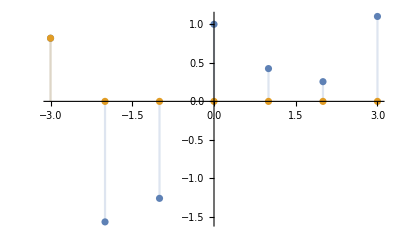

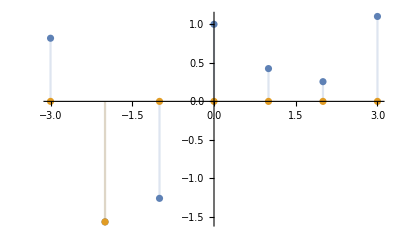

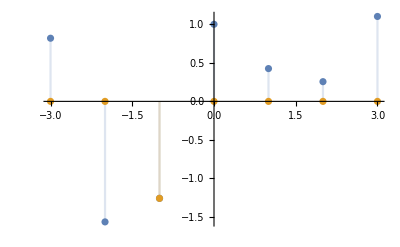

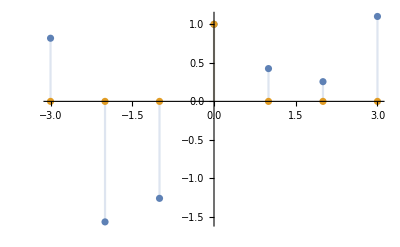

```mathematica
(*离散脉冲表示信号*)
ClearAll;
f[x_]:=Sin[x]+Cos[2x];
δ[x_]:=Piecewise[{{1,x==0},{0,x≠0}}];
DiscretePlot[{f[x],f[x] δ[x+3]},{x,-3,3}]
DiscretePlot[{f[x],f[x] δ[x+2]},{x,-3,3}]
DiscretePlot[{f[x],f[x] δ[x+1]},{x,-3,3}]
DiscretePlot[{f[x],f[x] δ[x]},{x,-3,3}]
```

```mathematica
(*离散卷积和*)
ClearAll;
x[n_]:=Piecewise[{{1, 0≤n≤4}, {0, n<0||n>4}}]
h[n_]:=Piecewise[{{1.2^n, 0≤n≤6}, {0, n<0||n>6}}]
y[n_,t_]:=Piecewise[{{∑_(k=n-6)^n h[n-k]x[k], n≤t}, {0, n>t}}]
Manipulate[DiscretePlot[{h[n-k],x[k],y[k,n]},{k,-8,11},PlotRange->{0,11}],{n,0,10,1}]
```

```mathematica
(*连续卷积和*)
ClearAll;
x[t_]:=Piecewise[{{1, 0≤t≤3}, {0, t<0||t>3}}]
h[t_]:=Piecewise[{{t, 0≤t≤6}, {0, t<0||t>6}}]
y[t_,T_]:=Piecewise[{{∫_(t-6)^t x[τ]h[t-τ]ⅆτ, t≤T}, {0, t>T}}]
Manipulate[Plot[{h[n-k],x[k],y[k,n]},{k,-8,11},PlotRange->{0,14}],{n,0,10}]
```